# How to make standing variation

## distribution of s from new mutation

In FGM the PDF of selective effects of new mutations relative to the wildtype, s = logW-logW_wt, is (Martin & Lenormand 2015)

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
```

This assumes a multivariate normal mutational distribution with no covariance (isotropy) and a symmetric Gaussian fitness landscape W.

In our case we are interested in a wildtype at the optimum, so=0

```mathematica
fs[s_,λ_,n_]:=Simplify[fs[s,0,λ,n],{s<0,λ>0}]
```

The remaining parameters are the mutational variance λ and the dimensionality of the landscape n. Note that we could alternatively use parameters n and Es, the expected selection coefficient against a mutation, by setting λ = 2 Es / n

-(2^(-n/2) ⅇ^((n s)/(2 Es)) (-(n s)/Es)^(n/2))/(s Gamma[n/2])

-Es

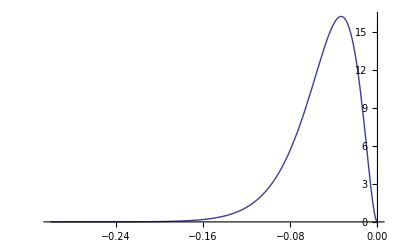

```mathematica
fs[s,λ,n]/.λ->2Es/n
Integrate[s%,{s,-∞,0},Assumptions->{Es>0,n>0}]
Plot[%%/.Es->0.05/.n->6,{s,-0.3,0},PlotRange->All]
```

Note that in two dimensions this is particularly simple

ⅇ^(s/Es)/Es

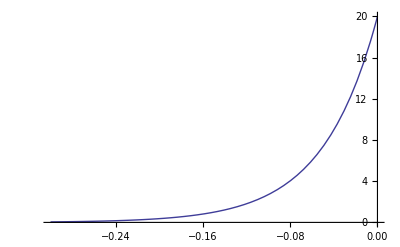

```mathematica
fs[s,λ,n]/.λ->2Es/n/.n->2
Plot[%/.Es->0.05,{s,-0.3,0},PlotRange->All]
```

ie -s is exponentially distributed with mean -Es

```mathematica
PDF[ExponentialDistribution[1/Es],-s]
Expectation[-s,s\[Distributed]ExponentialDistribution[1/Es]]
```

Piecewise[{{ⅇ^(s/Es)/Es, -s≥0}, {0, True}}]

-Es

## segregation times

For a continuous-time birth (λ) death (μ) process starting from N0 individuals (F[s,0]==s^N0) the PGF for the PDF of the number of individuals at time t can be solved for explicitly

```mathematica
fst=DSolve[{D[F[s,t],t]==D[F[s,t],s](λ s^2-(λ+μ)s+μ),F[s,0]==s^N0},F[s,t],{s,t}]//Flatten
```

{F[s,t]→((ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) μ)/(ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) λ))^N0}

Giving probability of extinction at time t

```mathematica
pextt=F[s,t]/.fst/.s->0//Factor//Simplify//FullSimplify
```

(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

Evaluating at s=0 as t goes to infinity gives the probabilty the lineage ever goes extinct. When birth rate is greater than death rate we have

```mathematica
pextinction=Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ>μ,μ>0}]
```

(μ/λ)^N0

and when death rate is greater than birth rate we have

```mathematica
Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ<μ,μ>0}]
```

1

The probability of persistence to time t is just one minus the probability of extinction by time t

```mathematica
pest=1-pextt
```

1-(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

From here on will we follow Uecker and Hermisson and let λ→(1+s)/2,μ→(1-s)/2 so that the continuous time branching process results match discrete time recursion equations.

We then get a probability of establishment that matches Haldane when s is small

```mathematica
1-pextinction/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1;
Series[%,{s,0,1}]//Normal
```

2 s

When |1/s| << 1/t << 1 (that is, at late times but while the mutant is still effectively neutral) the probability that a new mutant lineage persists to time t is approximately

```mathematica
pestapp1=Normal[Series[pest/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1/.s ->s ϵ^2/.t->t /ϵ,{ϵ,0,1}]]/.ϵ->1
```

2/t

And when -s t >>1, ie -s >> 1/t (that is, when the mutant is effectively deleterious) we have

```mathematica
pestapp2=Simplify[pest/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1]/. 1+ⅇ^(-s t) (-1+s)+s->ⅇ^(-s t) (-1+s)
```

(2 ⅇ^(s t) s)/(-1+s)

Visually check the small t (red) and large t (green) approximations of the full solution (blue)

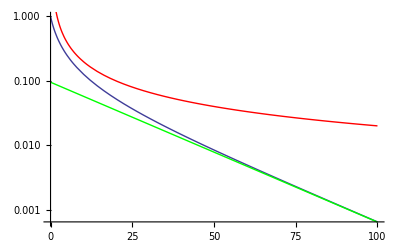

```mathematica
Show[
LogPlot[pest/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1/.s->-0.05,{t,0,100}],
LogPlot[pestapp1/.s->-0.05,{t,0,100},PlotRange->All,PlotStyle->Red],
LogPlot[pestapp2/.s->-0.05,{t,0,100},PlotRange->All,PlotStyle->Green]
]
```

When the mutation is weakly deleterious, -s<<1, but we look at late times so that 1/t << -s (together giving 1/t << -s << 1), the distribution of persistence times is exponential with parameter -s, giving mean persistence time -1/s

```mathematica
pestapp2/.-1+s->-1;
Integrate[%,{t,0,∞},Assumptions->s<0];
%%/%
%==Simplify[PDF[ExponentialDistribution[-s],t],t>0]
Expectation[t,t\[Distributed]ExponentialDistribution[-s]]
```

-ⅇ^(s t) s

True

-1/s

## probability mutation with effect s is segregating

Mutations that segregate longer are more likely to be in the standing genetic variation at any given time, given they appear. Here we use this logic to get the PDF of s in the standing variation:
f(s | segregating) = (Pr(segregating | s) f(s))/(∫Pr(segregating | s) f(s)ds). 

We will assume the probability of segregating given s is proportional to the expected segregation time given such a mutation arises, -1/s, as shown above. We then have, for n>2,

```mathematica
-1/s fs[s,λ,n];
Integrate[%,{s,-∞,0},Assumptions->{λ>0,n>2}];
%%/%
```

(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2])

This moves the distribution of s to smaller values:

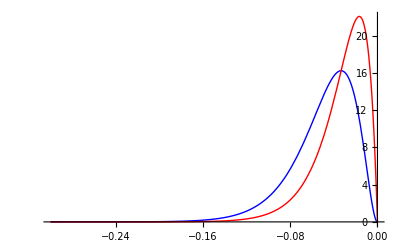

```mathematica
Show[
Plot[fs[s,λ,n]/.λ->2Es/n/.Es->0.05/.n->6,{s,-0.3,0},PlotStyle->Blue],
Plot[(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2])/.λ->2Es/n/.Es->0.05/.n->6,{s,-0.3,0},PlotStyle->Red],
PlotRange->All
]
```

When n≤2 the integral does not converge with small s and we are forced to approximate by integrating up to neutral mutations (-s<1/Ne, where Ne is the effective population size)

```mathematica
-1/s fs[s,λ,2];
Integrate[%,{s,-∞,-1/Ne},Assumptions->{λ>0,n<3,Ne>1}];
Simplify[%%/%,{s<0,λ>0,Ne>1}]
```

-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)])

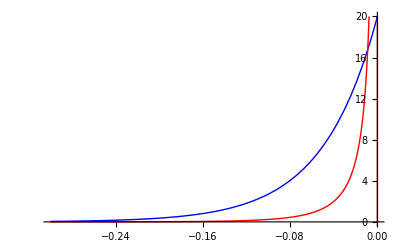

```mathematica
Show[
Plot[fs[s,λ,n]/.λ->2Es/n/.Es->0.05/.n->2,{s,-0.3,0},PlotStyle->Blue],
Plot[-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)])/.λ->2Es/n/.Es->0.05/.n->2/.Ne->10^4,{s,-0.3,1/10^4},PlotStyle->Red,PlotRange->{0,20}],
PlotRange->All
]
```

## distribution of mutation frequency given segregating

The probability that there is 1 individual at time t is

```mathematica
pn1=D[F[s,t]/.fst,{s,n}]/n!/.n->1/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

(4 ⅇ^(r t) r^2)/((-1+r+ⅇ^(r t) (1+r))^2)

and two individuals

```mathematica
pn2=D[F[s,t]/.fst,{s,n}]/n!/.n->2/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

(4 ⅇ^(r t) (-1+ⅇ^(r t)) r^2 (1+r))/((-1+r+ⅇ^(r t) (1+r))^3)

three

```mathematica
D[F[s,t]/.fst,{s,n}]/n!/.n->3/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

(4 ⅇ^(r t) (-1+ⅇ^(r t))^2 r^2 (1+r)^2)/((-1+r+ⅇ^(r t) (1+r))^4)

From this series we can see that we can write the probability of n individuals at time t like

```mathematica
pnt=pn1(pn2/pn1)^(n-1);
```

Check:

```mathematica
pnt/(D[F[s,t]/.fst,{s,n}]/n!)/.n->3/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

1

And dividing by the probability of survival to time t gives the conditional probability of having n individuals at time t given a mutant lineage lives to time t

```mathematica
pntgt=pnt/pest/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1/.r->s//FullSimplify
```

(2 s (1-(2 s)/(-1+s+ⅇ^(s t) (1+s)))^n)/((-1+ⅇ^(s t)) (1+s))

When t << -1/s  (effectively neutral) this is approximately

```mathematica
pntgtapp1=Normal[Series[pntgt/.s-> s ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
```

2 t^(-1+n) (2+t)^-n

which for large t (ie very neutral mutants) is approximately

```mathematica
pntgtapp1/. 2+t->t
```

2/t

Or when -1/s << t (ie deleterious mutants) we have approximately

```mathematica
pntgtapp2=pntgt/.-1+s+ⅇ^(s t) (1+s)->-1+s/.-1+ⅇ^(s t)->-1//Simplify
```

-(2 s ((1+s)/(1-s))^n)/(1+s)

Visually check small t (red) and large t (green) approximations against full solution (blue)

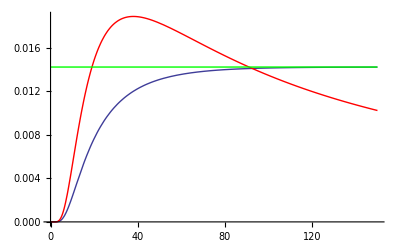

```mathematica
Show[
Plot[pntgt/.s->-0.05/.n->20,{t,0,150},PlotRange->All],
Plot[pntgtapp1/.s->-0.05/.n->20,{t,0,150},PlotRange->All,PlotStyle->Red],
Plot[pntgtapp2/.s->-0.05/.n->20,{t,0,150},PlotRange->All,PlotStyle->Green]
]
```

After long enough time all but wildtype mutations are effectviely deleterious (-1/s << t) and the PDF for the number of individuals in a lineage given it is segregating for a long time is

((1+s)/(1-s))^n Log[(1-s)/(1+s)]

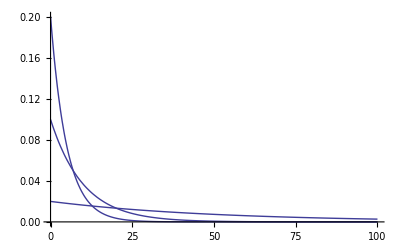

```mathematica
-(2 s ((1+s)/(1-s))^n)/(1+s);
Integrate[%,{n,0,∞},Assumptions->-1<s<0];
%%/%
Plot[%/.s->{-0.1,-0.05,-0.01},{n,0,100},PlotRange->All]
```

## converting s to a vector in phenotypic space

With a Gaussian fitness landscape with wildtype at the optimum, the selection coefficient of a mutation with phenotypic length r has selection coefficient

```mathematica
Simplify[Log[Exp[-r^2/2]]-Log[Exp[-0^2/2]],r>0]
```

-r^2/2

We can therefore solve for r

```mathematica
Simplify[Solve[s==-r^2/2,r][[1]],s<0]
```

{r→√2 √-s}

and with isotropic mutation we can uniformly choose a direction from the wildtype, meaning that we can place a mutation with effect s uniformly on the hypersphere with radius √(-2s).

For example, in 2-dimensional space we can choose a value in dimension 1 (x) uniformly between -√(-2s) and √(-2s). We then make the value in dimension 2 (y) equal to

```mathematica
Solve[x^2+y^2==r^2/.r->√2 √-s,y]
```

{{y→-√(-2 s-x^2)},{y→√(-2 s-x^2)}}

choosing the positive or negative with equal probability (Bernoulli with p=1/2).

## attempt to sample a mutation with n>2

With n>2 the PDF of s given segregation is

```mathematica
(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2]);
```

This gives CDF of the negative selection coefficient -s

1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)]

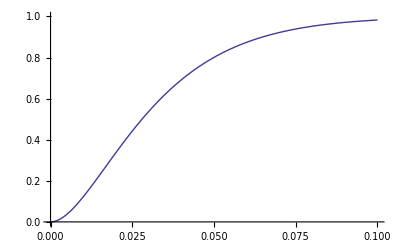

```mathematica
Integrate[(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2]),{s,-x,0},Assumptions->n>2]
Plot[%/.λ->2Es/n/.Es->0.05/.n->6,{x,0,0.1},PlotRange->{0,1}]
```

The inverse CDF is then

```mathematica
Solve[y==1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[y==1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)],x]

We can instead solve this numerically, below shows how doing this allows us to recreate the PDF

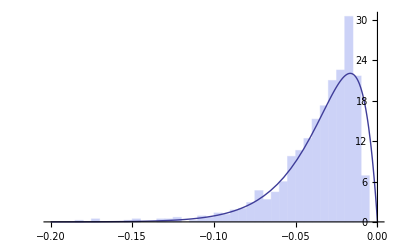

```mathematica
ntrials=1000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=6;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)]),{x,0.1}],{i,ntrials}];
Show[
Histogram[%,50,"PDF"],
Plot[(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2]),{s,-0.2,0},PlotRange->{0,200}],
PlotRange->{{-0.2,0},{0,All}},
AxesOrigin->{0,0}
]
Clear[Ne,λ,Es,n]
```

So now that we have chosen s, we need to convert to a point in n dimensions (equivalently, a vector from the origin). The first step is to get the length of the vector, which we have shown is just r=√(-2s)

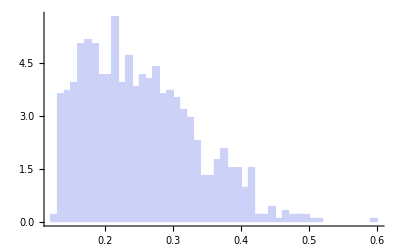

```mathematica
ntrials=1000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=6;
rand1=RandomReal[1,ntrials];
Table[√(2x)/.FindRoot[rand1[[i]]-(1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)]),{x,0.1}],{i,ntrials}];
Show[
Histogram[%,50,"PDF"],
PlotRange->{{0,1},{0,All}},
AxesOrigin->{0,0}
]
Clear[Ne,λ,Es,n]
```

We next want to put the point on the surface of the n dimensional hypersphere centered at the origin with radius r=√(-2s). It turns out we can do this by choosing n random normal variables (x1,x2,...xn) and transforming them into yi = r xi/√(Sum(xi^2,i)). This creates a uniform distribution over the surface of the hypersphere.

Lets look at this for n=3

```mathematica
ntrials=10000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=3;

rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)]),{x,0.1}],{i,ntrials}];
ss=Select[Chop[%],#<0&];
ntrials=Length[ss];
rs=√(-2ss);

Table[RandomVariate[NormalDistribution[],n],{i,ntrials}];
Table[Table[rs[[i]]%[[i,j]]/√Total[(%[[i]])^2],{j,n}],{i,ntrials}];
(*Table[√Total[(%[[i]])^2],{i,ntrials}]*)
ListPointPlot3D[%]

Clear[Ne,λ,Es,n]
```

-Graphics3D-

## attempt to sample a mutation with n=2

With n>2 the PDF of s given segregation is

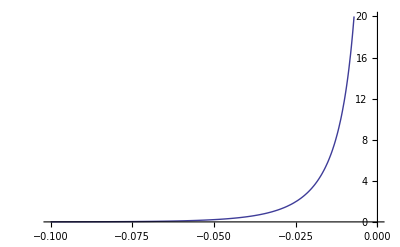

```mathematica
-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)]);
Plot[%/.λ->2Es/n/.Es->0.05/.n->6/.Ne->10^4,{s,-0.1,0},PlotRange->{0,20}]
```

This gives CDF of the negative selection coefficient -s

(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)]

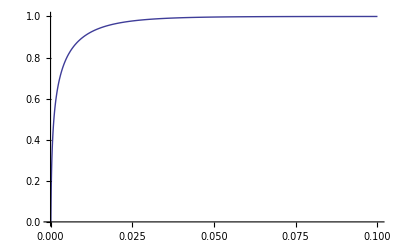

```mathematica
Integrate[-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)]),{s,-x,-1/Ne},Assumptions->{n≤2,1/x>Ne>1}]
Plot[%/.λ->2Es/n/.Es->0.05/.n->6/.Ne->10^4,{x,0,0.1},PlotRange->{0,1}]
```

The inverse CDF is then

```mathematica
Solve[y==(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[y==(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],x]

We can instead solve this numerically, below shows how doing this allows us to recreate the PDF

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

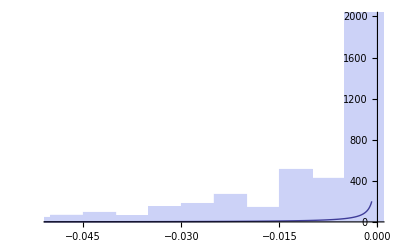

```mathematica
ntrials=10000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=2;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],{x,0.1}],{i,ntrials}];
Show[
Histogram[%,50],
Plot[-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)]),{s,-0.1,0},PlotRange->{0,200}],
PlotRange->{{-0.05,0},{0,2000}},
AxesOrigin->{0,0}
]
Clear[Ne,λ,Es,n]
```

And we can convert this to points in 2-dimensional space by drawing a random angle in [0,2π]

```mathematica
ntrials=10000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=2;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],{x,0.1}],{i,ntrials}];
ss=Select[%,#<0&];
ntrials=Length[ss];

RandomReal[2π,ntrials];
Table[{√(-2ss[[i]])Cos[%[[i]]],√(-2ss[[i]])Sin[%[[i]]]},{i,ntrials}];
DensityHistogram[%,50,"PDF",PlotRange->{{-1,1},{-1,1}},ChartLegends->Automatic]

Clear[Ne,λ,Es,n]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

Take a look at the cross-section

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

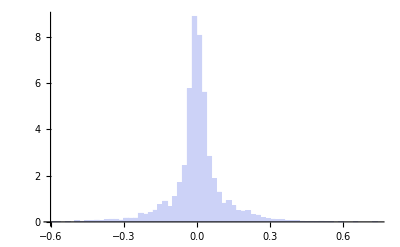

```mathematica
ntrials=10000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=2;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],{x,0.1}],{i,ntrials}];
ss=Select[%,#<0&];
ntrials=Length[ss];

RandomReal[2π,ntrials];
Table[√(-2ss[[i]])Cos[%[[i]]],{i,ntrials}];
Histogram[%,50,"PDF"]

Clear[Ne,λ,Es,n]
```

## choosing a mutation frequency

The PDF of lineage sizes given a mutation with selective effect s is segregating is

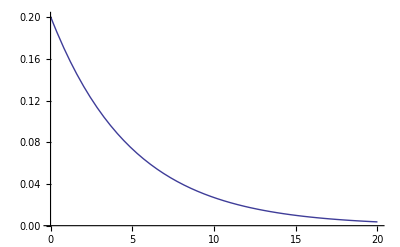

```mathematica
((1+s)/(1-s))^n Log[(1-s)/(1+s)];
Plot[%/.s->-0.1,{n,0,20},PlotRange->{0,All}]
```

This gives CDF

((-1+((1+s)/(1-s))^x) Log[(1-s)/(1+s)])/Log[(1+s)/(1-s)]

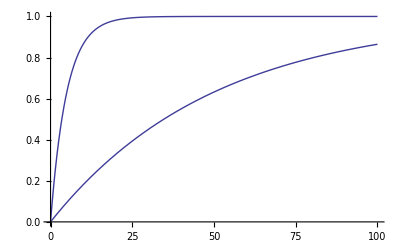

```mathematica
Integrate[((1+s)/(1-s))^n Log[(1-s)/(1+s)],{n,0,x}]
Plot[%/.s->{-0.1,-0.01},{x,0,100},PlotRange->{0,1}]
```

The inverse CDF is then

```mathematica
Simplify[Solve[y==((-1+((1+s)/(1-s))^x) Log[(1-s)/(1+s)])/Log[(1+s)/(1-s)],x]//Flatten,{-1<s<1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→Log[1+(y Log[(1+s)/(1-s)])/Log[(1-s)/(1+s)]]/Log[(1+s)/(1-s)]}

And we can then choose uniform random numbers to reproduce the PDF

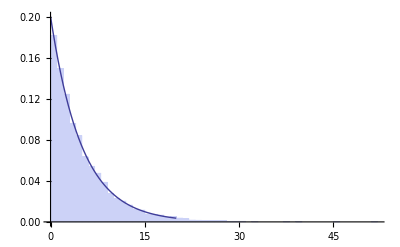

```mathematica
ntrials=10000;
s=-0.1;

RandomReal[1,ntrials];

Log[1+(% Log[(1+s)/(1-s)])/Log[(1-s)/(1+s)]]/Log[(1+s)/(1-s)];
Show[
Histogram[%,50,"PDF"],
Plot[((1+s)/(1-s))^n Log[(1-s)/(1+s)],{n,0,20}]
]
```

To convert to frequency we divide by the total population size.

## sample mutations and set their frequency, n=2

-Graphics-

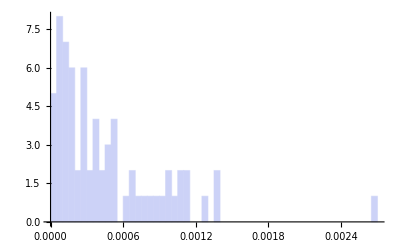

```mathematica
ntrials=100;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=2;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],{x,0.1}],{i,ntrials}];
ss=Select[%,#<0&];
ntrials=Length[ss];

RandomReal[2π,ntrials];
Table[{√(-2ss[[i]])Cos[%[[i]]],√(-2ss[[i]])Sin[%[[i]]]},{i,ntrials}];
DensityHistogram[%,50,"PDF",PlotRange->{{-1,1},{-1,1}},ChartLegends->Automatic]

RandomReal[1,ntrials];
Table[Log[1+(y Log[(1+s)/(1-s)])/Log[(1-s)/(1+s)]]/Log[(1+s)/(1-s)]/Ne/.s->ss[[i]]/.y->%[[i]],{i,ntrials}];
Histogram[%,50]

Clear[Ne,λ,Es,n]
```

-Graphics-

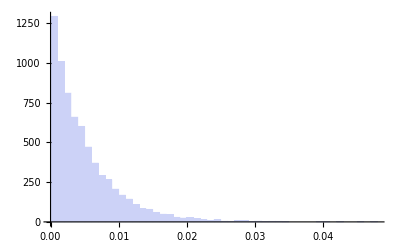

```mathematica
ntrials=10000;
Ne=10^3;
λ=2Es/n;
Es=0.05;
n=2;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],{x,0.1}],{i,ntrials}];
ss=Select[%,#<0&];
ntrials=Length[ss];

RandomReal[2π,ntrials];
Table[{√(-2ss[[i]])Cos[%[[i]]],√(-2ss[[i]])Sin[%[[i]]]},{i,ntrials}];
DensityHistogram[%,50,"PDF",PlotRange->{{-1,1},{-1,1}},ChartLegends->Automatic]

RandomReal[1,ntrials];
Table[Log[1+(y Log[(1+s)/(1-s)])/Log[(1-s)/(1+s)]]/Log[(1+s)/(1-s)]/Ne/.s->ss[[i]]/.y->%[[i]],{i,ntrials}];
Histogram[%,50]

Clear[Ne,λ,Es,n]
```

-Graphics-

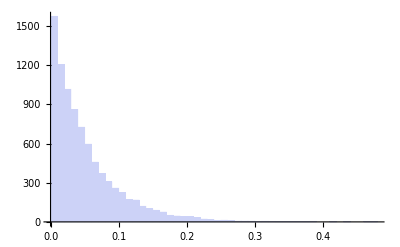

```mathematica
ntrials=10000;
Ne=10^2;
λ=2Es/n;
Es=0.05;
n=2;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],{x,0.1}],{i,ntrials}];
ss=Select[%,#<0&];
ntrials=Length[ss];

RandomReal[2π,ntrials];
Table[{√(-2ss[[i]])Cos[%[[i]]],√(-2ss[[i]])Sin[%[[i]]]},{i,ntrials}];
DensityHistogram[%,50,"PDF",PlotRange->{{-1,1},{-1,1}},ChartLegends->Automatic]

RandomReal[1,ntrials];
Table[Log[1+(y Log[(1+s)/(1-s)])/Log[(1-s)/(1+s)]]/Log[(1+s)/(1-s)]/Ne/.s->ss[[i]]/.y->%[[i]],{i,ntrials}];
Histogram[%,50]

Clear[Ne,λ,Es,n]
```

## just good old mutation-selection balance

```mathematica
Clear[s]
```

Assuming the population is primarily composed of wildtype, mutations of effect s ϵ [s, s+ds] arise at rate NT B U f(s) ds, where NT is the number of wildtype, B is the birth rate, U is the genomic mutation rate, and f(s) is the PDF of s from new mutations. These mutations change in number at per capita rate (1+s). Thus at equilibrium

```mathematica
Solve[ns==ns (1+s)+n U f ds,ns]
```

{{ns→-(ds f n U)/s}}

And converting to frequency gives

```mathematica
Solve[ps==ps (1+s)+ U f ds,ps]
```

{{ps→-(ds f U)/s}}

which is our classic μ/s.

(2^(-n/2) ds ⅇ^((n s)/(2 Es)) (-(n s)/Es)^(n/2) U)/(s^2 Gamma[n/2])

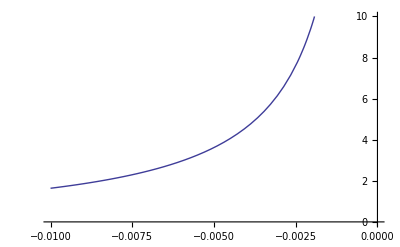

```mathematica
-(U fs[s,λ,n] ds)/s/.λ->2Es/n
Plot[%/.Es->0.05/.n->2/.U->0.001/.ds->1,{s,-0.01,0},PlotRange->{0,10}]
```

The above is a bit weird because I don’t know how to deal with the ds (e.g. why is the y-axis >1 when it should be frequency!!). But I think we can essentially make a new PDF that is weighted by mutation selection balance

```mathematica
-U/s fs[s,λ,2]
Integrate[%,{s,-∞,-1/Ne},Assumptions->{λ>0,n<3,Ne>1}];
Simplify[%%/%,{s<0,λ>0,Ne>1}]
```

-(ⅇ^(s/λ) U)/(s λ)

-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)])

## individual-based simulations

compare theory with distribution of s of individual mutations from individual-based simulation in python

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data/MSBalance_n2_K1000_alpha0.1_B2_u0.010.csv","Data"];
```

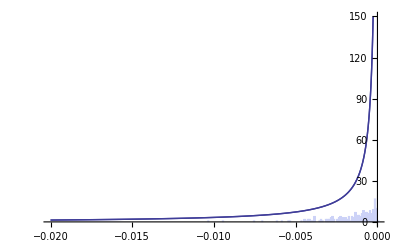

```mathematica
-(U NT B fs[s,λ,2]ds)/s;
%/.λ->2Es/n/.Es->0.05/.n->2/.ds->0.0001/.U->0.01/.NT->1000/.B->2;
theory=Plot[%,{s,-0.02,0},PlotRange->{0,150}];
Show[
theory,
Histogram[Select[data,MemberQ[#,10000]&][[All,2]],{0.0001}],
theory
]
```

We are dramatically overpredicting the number of mutations that we should see, perhaps negative epistasis is the problem? Lowering the mutation rate will mean less epistasis, but we still see the problem:

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data/MSBalance_n2_K1000_alpha0.1_B2_u0.001.csv","Data"];
```

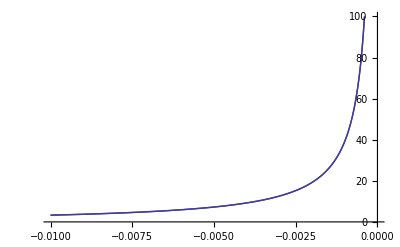

```mathematica
-(U NT B fs[s,λ,2]ds)/s;
%/.λ->2Es/n/.Es->0.05/.n->2/.ds->0.001/.U->0.001/.NT->1000/.B->2;
theory=Plot[%,{s,-0.01,0},PlotRange->{0,100}];
Show[
theory,
Histogram[Select[data,MemberQ[#,10000]&][[All,2]],{0.001}],
theory
]
```

if we instead look at the s of individuals (not individual mutations)

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data/MSBalance_n2_K1000_alpha0.1_B2_u0.010.csv","Data"];
```

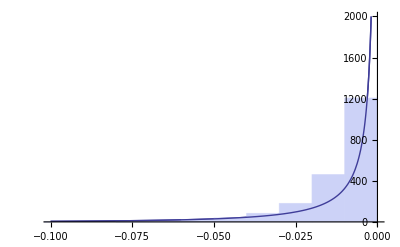

```mathematica
-(U NT B fs[s,λ,2]ds)/s;
%/.λ->2Es/n/.Es->0.05/.n->2/.ds->0.01/.U->0.01/.NT->1000/.B->2;
theory=Plot[%,{s,-0.1,0},PlotRange->{0,2000}];
Show[
theory,
Histogram[Select[data,MemberQ[#,10000]&][[All,2]],{0.01}],
theory
]
```

Notice that the selective effect of individuals is much greater (order of magnitude) than the selective effect of individual mutations -- meaning individuals tend to have more than one mutation and hence we need to consider a more complicated model with epistasis.

## modeling the simulation

The simulation starts with viability selection at the haploid stage (survive with probability w(s)) and random culling (to K haploid individuals). There is then random pairing of haploids, which go through meiosis with free recombination between all loci, and each of the two haploid products of meiosis become B individuals. Each individual then mutates at a unique locus with probability u, with effect drawn from a multivariate normal. The life-cycle then repeats.

So if we start a cycle with n(s)ds individuals with effect s ϵ [s,ds], we then expect to have n(s)w(s)ds after selection. We expect a total of ∫n(s)w(s)ds individuals after selection. We could use multinomial sampling (I think; difficult with continuous s) to distribution of the number after culling, but let’s instead assume K is large enough that we get the expected number, that is
K(n(s)w(s)ds)/(∫n(s)w(s)ds). Further, assume mutations are rare such that nearly all individuals are wildtype with s=0. Since w(0)=1, the expected number of individuals with s is then (K n(s) w(s) ds)/(n(0)). Given that wildtypes are expected to survive and have B offspring per parent, we expect n(0) before culling to be roughly BK, meaning the expected number of individuals with s should be roughly (n(s) w(s) ds)/B. With rare mutations an individual with effect s has a single mutation with effect s. When it mates with a wildtype half the 2B offspring then have effect s, making the expected number of individuals with effect s in the next generation  n(s) w(s) ds. When most individuals are wildtype the probability that a mutant mutates is low, and all new mutations arise from the wildtype. There are rouhgly K wildtypes, which each have B offspring, which each mutate to s with probability u f(s)ds. Thus we expect K B u f(s) ds individuals to arise anew each generation. Putting this together, we expect  n(s) w(s) ds + K B u f(s) ds individuals with s in the next generation (before selection and culling)	. This equals n(s), ie equilibrium, when

```mathematica
Solve[n ds==n w ds + k B u f ds,n]
```

{{n→-(B f k u)/(-1+w)}}

Survival probability is e^s, or roughly 1+s when s is small. This gives

```mathematica
Solve[n ds==n (1+s) ds + k B u f ds,n]//Simplify
```

{{n→-(B f k u)/s}}

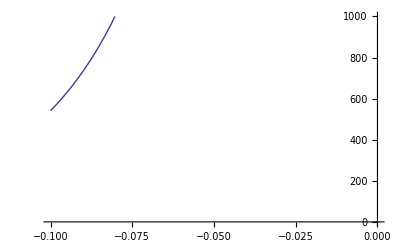

```mathematica
-(B k u fs[s,λ,n])/s;
%/.λ->2Es/n/.Es->0.05/.n->2/.u->0.01/.k->1000/.B->2;
Plot[%,{s,-0.1,0},PlotRange->{0,1000}]
```

## ode for 1d case

let x be the trait value and t be generation. let n[x,t] be the number of individuals with trait x in generation t. let w[x,t] be the expected number of offspring of an individual with trait x in generation t. let u[x] be the probability of a mutation that increases the trait value by x. then

```mathematica
n[x,t+1]==n[x,t]w[x,t]+u[] n[x]
```